## Delta-T noise in metal/spin flipper/metal junction

## ( Setup 1 : T_1, T_2, μ_1=μ_2=μ)

For incident electron with up spin

```mathematica
Remove["Global`*"];

(* a1= up incident to up reflection Subscript[r, uu], a2= up incident to down reflection Subscript[r, ud] *)    (* a3= up incident to up transmission Subscript[t, uu], a4= up incident to down transmission Subscript[t, ud] *)

a1=1;a2=0;a3=-1;a4=0;z1=-1;
b1=0;b2=1;b3=0;b4=-1;z2=0;
c1=1-I*J*m;c2=-I*J*F;c3=1;c4=0;z3=1+I*J*m;
d1=-I*J*F;d2=1+I*J*(m+1);d3=0;d4=1;z4=I*J*F;

{ruu,rud,tuu,tud}=Refine[LinearSolve[{{a1,a2,a3,a4},{b1,b2,b3,b4},{c1,c2,c3,c4},{d1,d2,d3,d4}},{z1,z2,z3,z4}],Element[Ed,Reals]]//FullSimplify;

{cruu,crud,ctuu,ctud}=FullSimplify[ComplexExpand[Conjugate[{ruu,rud,tuu,tud}]]];
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
ruu
rud
```

-(J (F^2 J+m (-2 ⅈ+J+J m)))/(4+J (2 ⅈ+J (F^2+m+m^2)))

(2 ⅈ F J)/(4+J (2 ⅈ+J (F^2+m+m^2)))

```mathematica
tuu
tud
```

(2 ⅈ (-2 ⅈ+J+J m))/(4+J (2 ⅈ+J (F^2+m+m^2)))

(2 ⅈ F J)/(4+J (2 ⅈ+J (F^2+m+m^2)))

For incident electron with down spin

```mathematica
a11=1;a21=0;a31=-1;a41=0; z11=-1;
b11=0;b21=1;b31=0;b41=-1;z21=0;
c11=1+I*J*m;c21=-I*J*F1;c31=1;c41=0;z31=1-I*J*m;
d11=-I*J*F1;d21=1-I*J(m-1);d31=0;d41=1;z41=I*J* F1;

{rdd,rdu,tdd,tdu}=Refine[LinearSolve[{{a11,a21,a31,a41},{b11,b21,b31,b41},{c11,c21,c31,c41},{d11,d21,d31,d41}},{z11,z21,z31,z41}],Element[Ed,Reals]]//FullSimplify;

{crdd,crdu,ctdd,ctdu}=FullSimplify[ComplexExpand[Conjugate[{rdd,rdu,tdd,tdu}]]];
```

```mathematica
rdd
rdu
```

-(J (F1^2 J+(2 ⅈ+J (-1+m)) m))/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

(2 ⅈ F1 J)/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

```mathematica
tdd
tdu
```

(4-2 ⅈ J (-1+m))/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

(2 ⅈ F1 J)/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

## Define functions

```mathematica
ruuN=-J1/(2 ⅈ+J1); tuuN= (2 ⅈ)/(2 ⅈ+J1);
```

```mathematica
rudN=0; tudN=0;  rduN=0; tduN=0;
```

```mathematica
rddN=J1/(2 ⅈ-J1); tddN= (2 ⅈ)/(2 ⅈ-J1);
```

```mathematica
F=Sqrt[(S-m)(S+m+1)];
F1=Sqrt[(S+m)(S-m+1)];
```

```mathematica
{Tuu,Tud,Tdu,Tdd}=ComplexExpand[Abs[{tuu,tud,tdu,tdd}]^2];
{Ruu,Rud,Rdu,Rdd}=ComplexExpand[Abs[{ruu,rud,rdu,rdd}]^2];

{RuuN,RudN,RduN,RddN}=ComplexExpand[Abs[{ruuN,rudN,rduN,rddN}]^2];
{TuuN,TudN,TduN,TddN}=ComplexExpand[Abs[{tuuN,tudN,tduN,tddN}]^2];
```

```mathematica
J=1/√(Ec)  (* Ec = (E/ c Subscript[J, 0]^2), c=6.56* 10^-2 *)
```

1/(√Ec)

```mathematica
J1=1/√(Ec1)  (* Ec1 = (E/c z) , z is the barrier strength *);
```

Thermovoltage functions

```mathematica
Ec∈Reals;  Ec1∈Reals;
```

```mathematica
FI1=Simplify[(Tuu),Element[Ec,Reals]];
FI2=Simplify[(Tuu+Tud),Element[Ec,Reals]];
FI3=Simplify[(Tdu+Tdd),Element[Ec,Reals]];
FI4=Simplify[(Tdd),Element[Ec,Reals]];
```

```mathematica
FI1s=Simplify[(Tuu),Element[Ec,Reals]];
FI2s=Simplify[(Tuu-Tud),Element[Ec,Reals]];
FI3s=Simplify[(Tdd-Tdu),Element[Ec,Reals]];
FI4s=Simplify[(Tdd),Element[Ec,Reals]];
```

```mathematica
FI1N=Simplify[(TuuN),Element[Ec1,Reals]];

DFI1N=D[FI1N,Ec1];
DFI12N=D[FI1N,{Ec1,2}];

DFI1N0=Limit[DFI1N,Ec1-> 0];
DFI12N0=Limit[DFI12N,Ec1-> 0];
```

```mathematica
DFI1=D[FI1,Ec];
DFI12=D[FI1,{Ec,2}];

DFI2=D[FI2,Ec];
DFI22=D[FI2,{Ec,2}];

DFI3=D[FI3,Ec];
DFI32=D[FI3,{Ec,2}];

DFI4=D[FI4,Ec];
DFI42=D[FI4,{Ec,2}];
```

```mathematica
DFI10=Limit[DFI1,Ec-> 0];
DFI120=Limit[DFI12,Ec-> 0];

DFI20=Limit[DFI2,Ec-> 0];
DFI220=Limit[DFI22,Ec-> 0];

DFI30=Limit[DFI3,Ec-> 0];
DFI320=Limit[DFI32,Ec-> 0];

DFI40=Limit[DFI4,Ec-> 0];
DFI420=Limit[DFI42,Ec-> 0];
```

```mathematica
DFI1s=D[FI1s,Ec];
DFI12s=D[FI1s,{Ec,2}];

DFI2s=D[FI2s,Ec];
DFI22s=D[FI2s,{Ec,2}];

DFI3s=D[FI3s,Ec];
DFI32s=D[FI3s,{Ec,2}];

DFI4s=D[FI4s,Ec];
DFI42s=D[FI4s,{Ec,2}];
```

```mathematica
DFI10s=Limit[DFI1s,Ec-> 0];
DFI120s=Limit[DFI12s,Ec-> 0];

DFI20s=Limit[DFI2s,Ec-> 0];
DFI220s=Limit[DFI22s,Ec-> 0];

DFI30s=Limit[DFI3s,Ec-> 0];
DFI320s=Limit[DFI32s,Ec-> 0];

DFI40s=Limit[DFI4s,Ec-> 0];
DFI420s=Limit[DFI42s,Ec-> 0];
```

```mathematica
S=0.5;
```

DeltaT noise functions

```mathematica
(*Define functions*)
Fuush=Ruu*Tuu+2*ComplexExpand[Re[cruu*tud*ctuu*rud]]+Rud*Tud;
Fudsh=ComplexExpand[Re[cruu*tuu*ctdd*rdd]]+2*ComplexExpand[Re[cruu*tud*ctdd*rdu]]+2*ComplexExpand[Re[ctuu*rud*crdd*tdu]]+2*ComplexExpand[Re[crud*tud*ctdu*rdu]];
Fddsh=Rdd*Tdd+2*ComplexExpand[Re[crdd*tdu*ctdd*rdu]]+Rdu*Tdu;
Fdush=ComplexExpand[Re[crdd*tdd*ctuu*ruu]]+2*ComplexExpand[Re[crdd*tdu*ctuu*rud]]+2*ComplexExpand[Re[ctdd*rdu*cruu*tud]]+2*ComplexExpand[Re[crdu*tdu*ctdd*rdd]];

Fuuth=(1-Ruu)^2+ComplexExpand[Re[cruu*rud*cruu*rud]]+(Rud)^2;
Fudth=(1-Rud) (1-Rdu)+2*ComplexExpand[Re[cruu*rud*crdd*rdu]]+Rud*Rdu;
Fduth=(1-Rdu) (1-Rud)+2*ComplexExpand[Re[crdd*rdu*cruu*rud]]+Rdu*Rud;
Fddth=(1-Rdd)^2+ComplexExpand[Re[crdd*rdu*crdd*rdu]]+(Rdu)^2;
```

```mathematica
FshN=RuuN*TuuN;
FthN=(1-RuuN)^2;
```

```mathematica
(* Derivatives of spin-flip contribution *)

DFuush=D[Fuush,Ec]; DFuush2=D[Fuush,{Ec,2}]; DFudsh=D[Fudsh,Ec];DFudsh2=D[Fudsh,{Ec,2}];
```

```mathematica
DFuuth=D[Fuuth,Ec]; DFuuth2=D[Fuuth,{Ec,2}]; DFudth=D[Fudth,Ec]; DFudth2=D[Fudth,{Ec,2}];
```

```mathematica
(* Derivatives of spin-flip contribution *)

DFddsh=D[Fddsh,Ec]; DFddsh2=D[Fddsh,{Ec,2}]; DFdush=D[Fdush,Ec];DFdush2=D[Fdush,{Ec,2}];
```

```mathematica
DFddth=D[Fddth,Ec]; DFddth2=D[Fddth,{Ec,2}]; DFduth=D[Fduth,Ec]; DFduth2=D[Fduth,{Ec,2}];
```

```mathematica
(* Derivatives of fnctions in NIN  *)

DFshN=D[FshN,Ec1]; DFshN2=D[FshN,{Ec1,2}]; DFthN=D[FthN,Ec1]; DFthN2=D[FthN,{Ec1,2}];
```

## Thermovoltage

```mathematica
(* spin up-down symmetry in spin-configurations  *)
Tuu/.{S-> 0.5,m->0.5,J0-> 0.5,Ec-> 0.1}
Tud/.{S-> 0.5,m->-0.5,J0-> 0.5,Ec-> 0.1}
Tdu/.{S-> 0.5,m->0.5,J0-> 0.5,Ec-> 0.1}
Tdd/.{S-> 0.5,m->-0.5,J0-> 0.5,Ec-> 0.1}
```

0.615385

0.232221

0.232221

0.615385

```mathematica
c=6.56* 10^-2;
```

```mathematica
(* NIN thermovoltage calculation *)
Subscript[cμI, s1N]= c j(DFI1N0/DFI12N0);   (* Subscript[cμI, s1N] = Subscript[μI, s1N] / Subscript[k, B] T̄,  j = c z/ Subscript[k, B] T̄ *)
Subscript[cμI, s1N0]=Subscript[cμI, s1N];
```

```mathematica
Subscript[cμI, s1N0]/.{j-> 0.3}
```

-0.00246

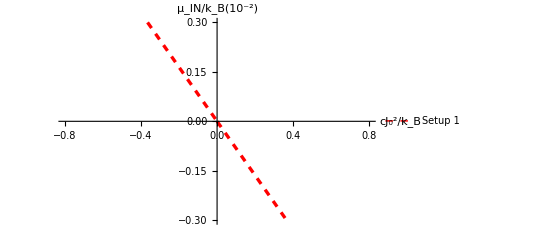

```mathematica
Plot[{Subscript[cμI, s1N0]*10^2},{j,-0.8,0.8},PlotRange->{-.3,.3},Exclusions->{0},PlotStyle->{{Red,Dashed,Thickness[0.006]},{Blue,Dashed,Thickness[0.006]},{Red,Dashed,Thickness[0.006]},{Magenta,Dotted,Thickness[0.006]}},AxesLabel-> {"cJ_0^2/k_B","μ_IN/k_B(10^-2)"},AxesStyle->Black,PlotLegends->Placed[{"Setup 1"},{Right,Bottom}],LabelStyle->{Bold,FontSize->17}]
```

## Charge and spin thermovoltage

```mathematica
Subscript[cμI, s1]=c j(DFI10/DFI120);
Subscript[cμI, s2]=c j(DFI20/DFI220);
Subscript[cμI, s3]=c j(DFI30/DFI320);
Subscript[cμI, s4]=c j(DFI40/DFI420);
```

```mathematica
Subscript[cμI, s10]=Subscript[cμI, s1]/.{S-> 0.5,m->0.5};
Subscript[cμI, s20]=Subscript[cμI, s2]/.{S-> 0.5,m->-0.5};
Subscript[cμI, s30]=Subscript[cμI, s3]/.{S-> 0.5,m->0.5};
Subscript[cμI, s40]=Subscript[cμI, s4]/.{S-> 0.5,m->-0.5};
```

```mathematica
Subscript[cμI, s1s]=c j(DFI10s/DFI120s);
Subscript[cμI, s2s]=c j(DFI20s/DFI220s);
Subscript[cμI, s3s]=c j(DFI30s/DFI320s);
Subscript[cμI, s4s]=c j(DFI40s/DFI420s);
```

```mathematica
Subscript[cμI, s10s]=Subscript[cμI, s1s]/.{S-> 0.5,m->0.5};
Subscript[cμI, s20s]=Subscript[cμI, s2s]/.{S-> 0.5,m->-0.5};
Subscript[cμI, s30s]=Subscript[cμI, s3s]/.{S-> 0.5,m->0.5};
Subscript[cμI, s40s]=Subscript[cμI, s4s]/.{S-> 0.5,m->-0.5};
```

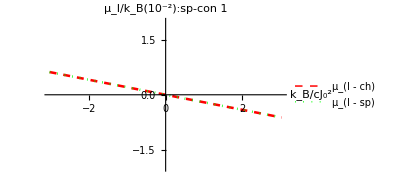
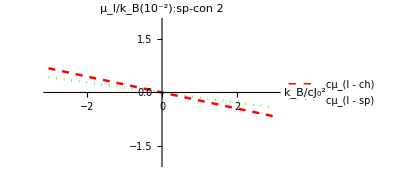

```mathematica
{Plot[{Subscript[cμI, s10]*100,Subscript[cμI, s10s]*100},{j,-3.02,3.02},PlotRange->{-2,2},PlotStyle->{{Red,Dashed,Thickness[0.006]},{Green,Dotted,Thickness[0.006]},{Blue,Dashed,Thickness[0.006]},{Magenta,Dotted,Thickness[0.006]}},AxesLabel-> {"k_B/cJ_0^2","μ_I/k_B(10^-2):sp-con 1"},AxesStyle->Black,PlotLegends->Placed[{"μ_(I - ch)","μ_(I - sp)"},{Right,Top}],LabelStyle->{Bold,FontSize->17}],Plot[{Subscript[cμI, s20]*100,Subscript[cμI, s20s]*100},{j,-3.02,3.02},PlotRange->{-2,2},PlotStyle->{{Red,Dashed,Thickness[0.006]},{Green,Dotted,Thickness[0.006]},{Blue,Dotted,Thickness[0.006]},{Magenta,Dotted,Thickness[0.006]}},AxesLabel-> {"k_B/cJ_0^2","μ_I/k_B(10^-2):sp-con 2"},AxesStyle->Black,PlotLegends->Placed[{"cμ_(I - ch)","cμ_(I - sp)"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]}
```

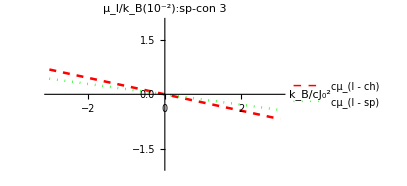
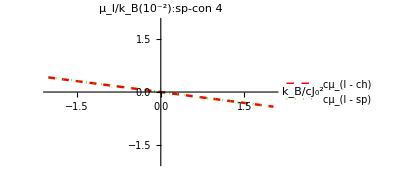

```mathematica
{Plot[{Subscript[cμI, s30]*100,Subscript[cμI, s30s]*100},{j,-3.02,3.02},PlotRange->{-2,2},PlotStyle->{{Red,Dashed,Thickness[0.006]},{Green,Dotted,Thickness[0.006]},{Blue,Dotted,Thickness[0.006]},{Magenta,Dotted,Thickness[0.006]}},AxesLabel-> {"k_B/cJ_0^2","μ_I/k_B(10^-2):sp-con 3"},AxesStyle->Black,PlotLegends->Placed[{"cμ_(I - ch)","cμ_(I - sp)"},{Right,Top}],LabelStyle->{Bold,FontSize->17}],Plot[{Subscript[cμI, s40]*100,Subscript[cμI, s40s]*100},{j,-2.02,2.02},PlotRange->{-2,2},PlotStyle->{{Red,Dashed,Thickness[0.006]},{Green,Dotted,Thickness[0.006]},{Blue,Dashed,Thickness[0.006]},{Magenta,Dotted,Thickness[0.006]}},AxesLabel-> {"k_B/cJ_0^2","μ_I/k_B(10^-2):sp-con 4"},AxesStyle->Black,PlotLegends->Placed[{"cμ_(I - ch)","cμ_(I - sp)"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]}
```

## Δ_T noise

```mathematica
ΔT=T1-T2;
T̄=(T1+T2)/2;
```

```mathematica
k=8.617*10^-5
```

0.00008617

```mathematica
Ec=Ed *(k*T̄) /c j; 
Ec1=Ed *(k*T̄) /c j;
```

```mathematica
(*Define substitutions*)

sub1={Ed->Subscript[cμI, s10]};
sub2={Ed->Subscript[cμI, s20]};
sub3={Ed->Subscript[cμI, s30]};
sub4={Ed->Subscript[cμI, s40]};

sub1s={Ed->Subscript[cμI, s10s]};
sub2s={Ed->Subscript[cμI, s20s]};
sub3s={Ed->Subscript[cμI, s30s]};
sub4s={Ed->Subscript[cμI, s40s]};

subN={Ed->Subscript[cμI, s1N0]};
```

```mathematica
{FshNv1,DFsh2Nv1}={FshN,DFshN2}/.subN;
{FthNv1,DFth2Nv1}={FthN,DFthN2}/.subN;
```

```mathematica
xv=(k*T̄)/c j;
```

```mathematica
ScN=4((2((π^2-6)/9)FshNv1-xv^2*DFsh2Nv1*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(FshNv1*(7*π^4-75*π^2+90)/675- xv^2*DFsh2Nv1*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
SsN=(2 ScN/.{T1->4,T2->3});
```

```mathematica
SthN=(FthNv1+xv^2*DFth2Nv1(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFth2Nv1(π^2/6));
StN=(SthN/.{ T1->4,T2->3});
```

Δμ spin-con 1 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv1,DFuush2v1}={Fuush,DFuush2}/.sub1;
{Fudshv1,DFudsh2v1}={Fudsh,DFudsh2}/.sub1;
```

```mathematica
{Fuuthv1,DFuuthv1,DFuuth2v1}={Fuuth,DFuuth,DFuuth2}/.sub1;
{Fudthv1,DFudthv1,DFudth2v1}={Fudth,DFudth,DFudth2}/.sub1;
```

```mathematica
Suuc1=4((2((π^2-6)/9)Fuushv1-xv^2*DFuush2v1*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(Fuushv1*(7*π^4-75*π^2+90)/675- xv^2*DFuush2v1*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssuu1=(Suuc1/.{S->0.5,m->0.5,T1->4,T2->3});
```

```mathematica
Suut1=(Fuuthv1+xv^2*DFuuth2v1(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFuuth2v1(π^2/6));
```

```mathematica
Stuu1=(Suut1/.{S->0.5,m->0.5, T1->4,T2->3});
```

Δμ spin-con 2 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv2,DFuush2v2}={Fuush,DFuush2}/.sub2;
{Fudshv2,DFudsh2v2}={Fudsh,DFudsh2}/.sub2;

{Fuuthv2,DFuuthv2,DFuuth2v2}={Fuuth,DFuuth,DFuuth2}/.sub2;
{Fudthv2,DFudthv2,DFudth2v2}={Fudth,DFudth,DFudth2}/.sub2;
```

```mathematica
Subscript[cμI, s2]/.{S->0.5,m->-0.5}
```

-0.00225 j

```mathematica
Suuc2=4((2((π^2-6)/9)Fuushv2-xv^2*DFuush2v2*(π^2(7 π^2-60)/45))* (ΔT/(2*T̄))^2+((2/3)(Fuushv2*(7*π^4-75*π^2+90)/675- xv^2*DFuush2v2*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
Sudc2=4((2(-(π^2-6)/9)Fudshv2+xv^2*DFudsh2v2*(π^2(7 π^2-60)/45))* (ΔT/(2*T̄))^2+((2/3)(-Fudshv2*(7*π^4-75*π^2+90)/675+ xv^2*DFudsh2v2*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssuu2=(Suuc2/.{S->0.5,m->-0.5,T1->4,T2->3});
Ssud2=(Sudc2/.{S->0.5,m->-0.5, T1->4,T2->3});
```

```mathematica
Suut2=-(Fuuthv2+xv^2*DFuuth2v2(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFuuth2v2(π^2/6));
Sudt2=-(Fudthv2+xv^2*DFudth2v2(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFudth2v2(π^2/6));
```

```mathematica
Stuu2=(Suut2/.{S->0.5,m->-0.5, T1->4,T2->3});
Stud2=(Sudt2/.{S->0.5,m->-0.5, T1->4,T2->3});
```

Δμ spin-con 3 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fddshv3,DFddsh2v3}={Fddsh,DFddsh2}/.sub3;
{Fdushv3,DFdush2v3}={Fdush,DFdush2}/.sub3;

{Fddthv3,DFddthv3,DFddth2v3}={Fddth,DFddth,DFddth2}/.sub3;
{Fduthv3,DFduthv3,DFduth2v3}={Fduth,DFduth,DFduth2}/.sub3;
```

```mathematica
Subscript[cμI, s30]/.{S->0.5,m->0.5}
```

-0.00225 j

```mathematica
Sddc3=4((2((π^2-6)/9)Fddshv3-xv^2*DFddsh2v3*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(Fddshv3*(7*π^4-75*π^2+90)/675- xv^2*DFddsh2v3*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
Sduc3=4((2(-(π^2-6)/9)Fdushv3+xv^2*DFdush2v3*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2+((2/3)(-Fdushv3*(7*π^4-75*π^2+90)/675+ xv^2*DFdush2v3*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssdd3=(Sddc3/.{S->0.5,m->0.5,T1->4,T2->3});
```

```mathematica
Ssdu3=(Sduc3/.{S->0.5,m->0.5, T1->4,T2->3});
```

```mathematica
Sddt3=-(Fddthv3+xv^2*DFddth2v3(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFddth2v3(π^2/6));
Sdut3=-(Fduthv3+xv^2*DFduth2v3(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFduth2v3(π^2/6));
```

```mathematica
Stdd3=(Sddt3/.{S->0.5,m->0.5, T1->4,T2->3});
Stdu3=(Sdut3/.{S->0.5,m->0.5, T1->4,T2->3});
```

Δμ spin-con 4 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fddshv4,DFddsh2v4}={Fddsh,DFddsh2}/.sub4;
{Fdushv4,DFdush2v4}={Fdush,DFdush2}/.sub4;

{Fddthv4,DFddthv4,DFddth2v4}={Fddth,DFddth,DFddth2}/.sub4;
{Fduthv4,DFduthv4,DFduth2v4}={Fduth,DFduth,DFduth2}/.sub4;
```

```mathematica
Subscript[cμI, s40]/.{S->0.5,m->0.5}
```

-0.00205 j

```mathematica
Sddc4=4((2((π^2-6)/9)Fddshv4-xv^2*DFddsh2v4*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(Fddshv4*(7*π^4-75*π^2+90)/675- xv^2*DFddsh2v4*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssdd4=(Sddc4/.{S->0.5,m->-0.5,T1->4,T2->3});
```

```mathematica
Sddt4=-(Fddthv4+xv^2*DFddth2v4(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFddth2v4(π^2/6));
```

```mathematica
Stdd4=(Sddt4/.{S->0.5,m->-0.5, T1->4,T2->3});
```

Charge Δ_T noise : Δμ spin-con ( for spin  flip Δ_T noise)

```mathematica
Duush=(Ssuu1+Ssuu2);
Dudsh=(Ssud2);
Dddsh=(Ssdd3+Ssdd4);
Ddush=(Ssdu3);
Dlcuush= (Duush+Dudsh+Dddsh+Ddush);
```

```mathematica
Duuth=(Stuu1+Stuu2);
Dudth=(Stud2);
Dddth=(Stdd3+Stdd4);
Dduth=(Stdu3);
Dlcuuth=(Duuth+Dudth +Dddth+Dduth );
```

## Spin Δ_T noise

spin Δμ spin-con 1 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv1s,DFuush2v1s}={Fuush,DFuush2}/.sub1s;
{Fudshv1s,DFudsh2v1s}={Fudsh,DFudsh2}/.sub1s;

{Fuuthv1s,DFuuthv1s,DFuuth2v1s}={Fuuth,DFuuth,DFuuth2}/.sub1s;
{Fudthv1s,DFudthv1s,DFudth2v1s}={Fudth,DFudth,DFudth2}/.sub1s;
```

```mathematica
Suuc1s=4((2((π^2-6)/9)Fuushv1s-xv^2*DFuush2v1s*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(Fuushv1s*(7*π^4-75*π^2+90)/675- xv^2*DFuush2v1s*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssuu1s=(Suuc1s/.{S->0.5,m->0.5,T1->4,T2->3});
```

```mathematica
Suut1s=-(Fuuthv1s+xv^2*DFuuth2v1s(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFuuth2v1s(π^2/6));
```

```mathematica
Stuu1s=(Suut1s/.{S->0.5,m->0.5, T1->4,T2->3});
```

```mathematica
Ssuu1s/.{S->0.5,m->-0.5,j->1.2,Ed-> 0.01}
```

0.00252335

Δμ spin-con 2 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv2s,DFuush2v2s}={Fuush,DFuush2}/.sub2s;
{Fudshv2s,DFudsh2v2s}={Fudsh,DFudsh2}/.sub2s;

{Fuuthv2s,DFuuthv2s,DFuuth2v2s}={Fuuth,DFuuth,DFuuth2}/.sub2s;
{Fudthv2s,DFudthv2s,DFudth2v2s}={Fudth,DFudth,DFudth2}/.sub2s;
```

```mathematica
Subscript[cμI, s2s]/.{S->0.5,m->-0.5}
```

-0.00141923 j

```mathematica
Suuc2s=4((2((π^2-6)/9)Fuushv2s-xv^2*DFuush2v2s*(π^2(7 π^2-60)/45))* (ΔT/(2*T̄))^2+((2/3)(Fuushv2s*(7*π^4-75*π^2+90)/675- xv^2*DFuush2v2s*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
Sudc2s=4((2(-(π^2-6)/9)Fudshv2s+xv^2*DFudsh2v2s*(π^2(7 π^2-60)/45))* (ΔT/(2*T̄))^2+((2/3)(-Fudshv2s*(7*π^4-75*π^2+90)/675+ xv^2*DFudsh2v2s*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssuu2s=(Suuc2s/.{S->0.5,m->-0.5,T1->4,T2->3});
```

```mathematica
Ssud2s=(Sudc2s/.{S->0.5,m->-0.5, T1->4,T2->3});
```

```mathematica
Suut2s=-(Fuuthv2s+xv^2*DFuuth2v2s(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFuuth2v2s(π^2/6));
Sudt2s=-(Fudthv2s+xv^2*DFudth2v2s(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFudth2v2s(π^2/6));
```

```mathematica
Stuu2s=(Suut2s/.{S->0.5,m->-0.5, T1->4,T2->3});
Stud2s=(Sudt2s/.{S->0.5,m->-0.5, T1->4,T2->3});
```

Δμ spin-con 3 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fddshv3s,DFddsh2v3s}={Fddsh,DFddsh2}/.sub3s;
{Fdushv3s,DFdush2v3s}={Fdush,DFdush2}/.sub3s;

{Fddthv3s,DFddthv3s,DFddth2v3s}={Fddth,DFddth,DFddth2}/.sub3s;
{Fduthv3s,DFduthv3s,DFduth2v3s}={Fduth,DFduth,DFduth2}/.sub3s;
```

```mathematica
Sddc3s=4((2((π^2-6)/9)Fddshv3s-xv^2*DFddsh2v3s*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(Fddshv3s*(7*π^4-75*π^2+90)/675- xv^2*DFddsh2v3s*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
Sduc3s=4((2(-(π^2-6)/9)Fdushv3+xv^2*DFdush2v3s*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2+((2/3)(-Fdushv3s*(7*π^4-75*π^2+90)/675+ xv^2*DFdush2v3s*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssdd3s=(Sddc3s/.{S->0.5,m->0.5,T1->4,T2->3});
Ssdu3s=(Sduc3s/.{S->0.5,m->0.5, T1->4,T2->3});
```

```mathematica
Sddt3s=-(Fddthv3s+xv^2*DFddth2v3s(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFddth2v3s(π^2/6));
Sdut3s=-(Fduthv3s+xv^2*DFduth2v3s(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFduth2v3s(π^2/6));
```

```mathematica
Stdd3s=(Sddt3s/.{S->0.5,m->0.5, T1->4,T2->3});
Stdu3s=(Sdut3s/.{S->0.5,m->0.5, T1->4,T2->3});
```

```mathematica
Fduth/.{S->0.5,m->0.5,J0->1.2,Ed-> 0.01};
```

Δμ spin-con 4 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fddshv4s,DFddsh2v4s}={Fddsh,DFddsh2}/.sub4s;
{Fdushv4s,DFdush2v4s}={Fdush,DFdush2}/.sub4s;

{Fddthv4s,DFddthv4s,DFddth2v4s}={Fddth,DFddth,DFddth2}/.sub4s;
{Fduthv4s,DFduthv4s,DFduth2v4s}={Fduth,DFduth,DFduth2}/.sub4s;
```

```mathematica
Sddc4s=4((2((π^2-6)/9)Fddshv4s-xv^2*DFddsh2v4s*(π^2(7 π^2-60)/90))* (ΔT/(2*T̄))^2-((2/3)(Fddshv4s*(7*π^4-75*π^2+90)/675- xv^2*DFddsh2v4s*((294-31π^2)/630)))*(ΔT/(2*T̄))^4);
```

```mathematica
Ssdd4s=(Sddc4s/.{S->0.5,m->-0.5,T1->4,T2->3});
```

```mathematica
Sddt4s=-(Fddthv4s+xv^2*DFddth2v4s(π^2/3)+(ΔT/2 T̄)^2*xv^2*DFddth2v4s(π^2/6));
```

```mathematica
Stdd4s=(Sddt4s/.{S->0.5,m->-0.5, T1->4,T2->3});
```

Spin Δ_T noise for Δμ spin-con ( for spin  flip Δ_T noise)

```mathematica
Duushs=(Ssuu1s+Ssuu2s);
Dudshs=(Ssud2s);
Dddshs=(Ssdd3s+Ssdd4s);
Ddushs=(Ssdu3s);
Dlcuushs=(Duushs-Dudshs-Ddushs+Dddshs);
```

```mathematica
Duuths=(Stuu1s+Stuu2s);
Dudths=(Stud2s);
Dddths=(Stdd3s+Stdd4s);
Dduths=(Stdu3s);
Dlcuuths=Duuths-Dudths+Dddths-Dduths;
```

In the approximation limit (k_B T̄/cJ_0^2) << 1

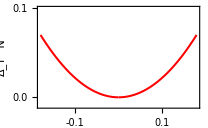

```mathematica
Plot2=Plot[{(SsN +StN )},{j,-.19,0.19},PlotRange->{-0.01,.1},Frame->True,FrameStyle->Thickness[0.002],Axes->False,PlotStyle->{{Red,Thickness[0.007]}},FrameTicksStyle->Directive[Black,10,Bold],FrameTicks->{{{{0,"0.0"},{0.1,"0.1"},{0.5,"0.5"}},None},{{{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",10,Black,Bold],Style["Δ_T^N",10,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

```mathematica
Plot of Subscript[Δ, T]^η noise in unit of (2 e^2(Subscript[k, B] T̄))/h for setup 2 given in Fig. 5(a)
```

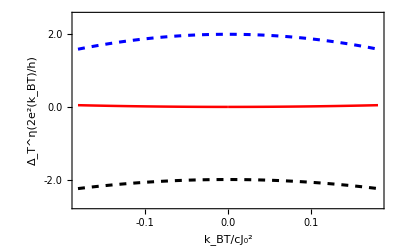

```mathematica
Plot[{(Dlcuush +Dlcuuth),(Dlcuushs+Dlcuuths),(SsN +StN )},{j,-.19,0.19},PlotRange->{-2.7,2.5},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0055]},{Blue,Dashed,Thickness[0.0055]},{Red,Thickness[0.0045]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-2,"-2.0"},{0,"0.0"},{2,"2.0"}},None},{{{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["Δ_T^η(2e^2(k_BT̄)/h)",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

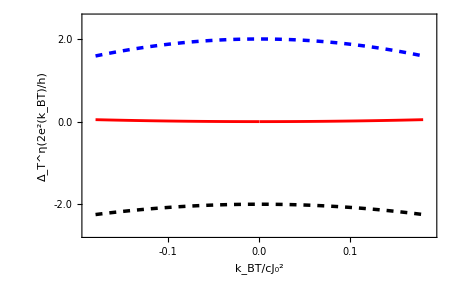

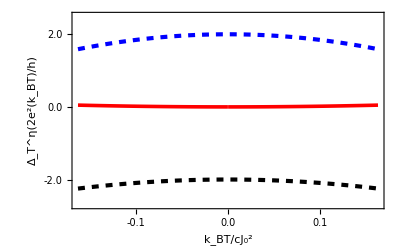

```mathematica
Plot[{(Dlcuushs+Dlcuuth),(Dlcuushs+Dlcuuths),(SsN +StN )},{j,-.19,0.19},PlotRange->{-2.7,2.5},Frame->True,FrameStyle->Thickness[0.0046],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0075]},{Red,Thickness[0.0065]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-2,"-2.0"},{-4,"-4.0"},{0,"0.0"},{4,"4.0"},{2,"2.0"}},None},{{{-4,"-4.0"},{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"},{4,"4.0"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["Δ_T^η(2e^2(k_BT̄)/h)",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

```mathematica
Plot of Subscript[Δ, Tsh(th)]^η noise in unit of (2 e^2(Subscript[k, B] T̄))/h for setup 2 given in Fig. 9(a)
```

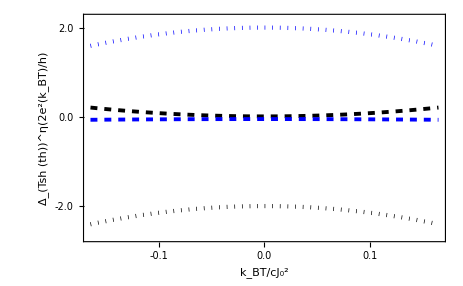

```mathematica
Plot[{Dlcuush,Dlcuuth,Dlcuushs ,Dlcuuths},{j,-0.19,0.19},PlotRange->{-2.7,2.2},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.006]},{Black,Dotted,Thickness[0.0065]},{Blue,Dashed,Thickness[0.006]},{Blue,Dotted,Thickness[0.0065]},{Red,Dashed,Thickness[0.007]},{Red,Dotted,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-2,"-2.0"},{-4,"-4.0"},{0,"0.0"},{2,"2.0"}},None},{{{-8,"-8.0"},{-0.1,"-0.1"},{0,"0.0"},{.1,"0.1"},{4,"4.0"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["Δ_(Tsh (th))^η(2e^2(k_BT̄)/h)",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

## Ratio Δ_Tsh^η/Δ_Tth^η

```mathematica
Rch=Abs[Dlcuush/Dlcuuth];
```

```mathematica
RN=(SsN/StN);
```

```mathematica
Rsp=Abs[(Dlcuushs )/Dlcuuths];
```

```mathematica
Plot of ratio |Subscript[Δ, Tsh]^η/Subscript[Δ, Tth]^η| noise  for setup 2 given in Fig. 5(b)
```

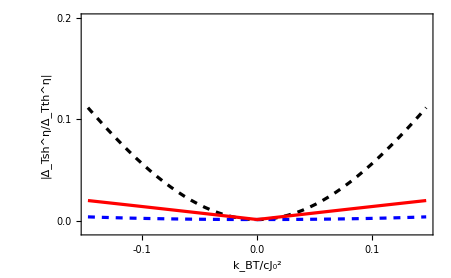

```mathematica
Plot[{Rch,Rsp,RN},{j,-.19,.19},PlotRange->{-0.01,0.2},Frame->True,FrameStyle->Thickness[0.0046],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0051]},{Blue,Dashed,Thickness[0.0051]},{Red,Thickness[0.0051]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-2,"-2.0"},{-4,"-4.0"},{0,"0.0"},{0.2,"0.2"},{0.1,"0.1"}},None},{{{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["|Δ_Tsh^η/Δ_Tth^η|",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```